# S2S Data Cutting

## Slide Show Subtitle

BX Pan
2017.9.27

Environment Setting

```mathematica
controlDirectory="/Volumes/lambda/Data/S2S/Control/";
pertubationDirectory="/Volumes/lambda/Data/S2S/Pertubation/";
```

```mathematica
polygon=Block[{westconus},
	westconus=Block[{ow,ca},
	ow=Import["/Users/lambda/Documents/Data/GeoDivision/CONUS/oregonwashington.mx"];
	ca=Import["/Users/lambda/Documents/Data/GeoDivision/CONUS/california.mx"];
	Polygon[Flatten[{ow[[1]],ca[[1]]},1]]];
	westconus[[1]]];
(*polygon in the form of {subpoly1,subpoly2,...},subpoly in th form of {{long1,lat1},{long2,lat2}...}*)
```

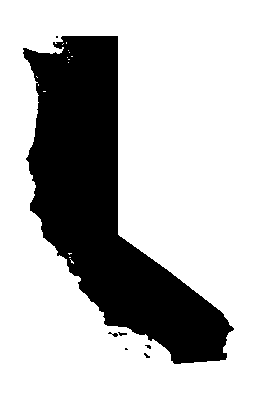

```mathematica
Graphics[Polygon[polygon]]
```

S2SCut

```mathematica
S2Scut[polygon_,dataset_]:=Block[{points,sample,result,files,sindex,scale},
 SetDirectory["/Volumes/lambda/Data/S2S/Control/"<>dataset];
 sample=FileNames["*.nc"][[1]];
 points=Block[{s2sprecip,s2slat,s2slon,s2stime,p,indexes},
	{s2sprecip,s2slat,s2slon,s2stime}=Map[Import[sample,{"Datasets",#}]&,{"tp","latitude","longitude","time"}];
    p=Block[{InOrOut,grids},
        InOrOut[point_]:=Block[{singletest},
			singletest[poly_] := Round[(Total@ Mod[(# - RotateRight[#]) &@(ArcTan @@ (point - #) & /@ poly), 2 Pi, -Pi]/2/Pi)] != 0;
			(Map[singletest,polygon])/.List->Or];
        grids=Block[{scope=Map[MinMax,Transpose[Flatten[polygon,1]]],lat,lon},
            lat=Select[s2slat,And[#<=scope[[2,2]], #>=scope[[2,1]]]&];
            lon=Select[s2slon,And[#<=scope[[1,2]], #>=scope[[1,1]]]&];
        Table[Table[{lat[[i]],lon[[j]]},{j,Length[lon]}],{i,Length[lat]}]];
        Select[Flatten[grids,1],InOrOut[Reverse[#]]&]];
    indexes=Block[{grids=Table[Table[{s2slat[[i]],s2slon[[j]]},{j,Length[s2slon]}],{i,Length[s2slat]}]},
        Map[Position[grids,#][[1]]&,p]];
    indexes];
 sindex=Position[Map[Flatten[#/.Rule->List]&,Import[sample,"Annotations"]],
	_?(MemberQ[#,"Total Precipitation"]&)][[1,1]];
 files=FileNames["*.nc"];
 scale=Map[Import[#,"Annotations"][[sindex,1;;2,2]]&,files];
 result=Block[{raw=Map[Block[{d=Import[#,{"Datasets","tp"}]},
          Table[d[[;;,points[[jj,1]],points[[jj,2]]]],{jj,Length[points]}]]&,files]},
          Table[raw[[i]]*scale[[i,1]]+scale[[i,2]],{i,Length[scale]}]];
 Export[dataset<>".mx",result];
 result];
```

```mathematica
SetDirectory["/Volumes/lambda/Data/S2S/Control/"];
names=FileNames[][[{1,3,4,5,6,7,8,9,10,11}]]
```

```mathematica
PS2Scut[polygon_,dataset_]:=Block[{points,sample,result,files,sindex,scale},
 SetDirectory["/Volumes/lambda/Data/S2S/Pertubation/"<>dataset];
 sample=FileNames["*.nc"][[1]];
 points=Block[{s2sprecip,s2slat,s2slon,s2stime,p,indexes},
	{s2sprecip,s2slat,s2slon,s2stime}=Map[Import[sample,{"Datasets",#}]&,{"tp","latitude","longitude","time"}];
    p=Block[{InOrOut,grids},
        InOrOut[point_]:=Block[{singletest},
			singletest[poly_] := Round[(Total@ Mod[(# - RotateRight[#]) &@(ArcTan @@ (point - #) & /@ poly), 2 Pi, -Pi]/2/Pi)] != 0;
			(Map[singletest,polygon])/.List->Or];
        grids=Block[{scope=Map[MinMax,Transpose[Flatten[polygon,1]]],lat,lon},
            lat=Select[s2slat,And[#<=scope[[2,2]], #>=scope[[2,1]]]&];
            lon=Select[s2slon,And[#<=scope[[1,2]], #>=scope[[1,1]]]&];
        Table[Table[{lat[[i]],lon[[j]]},{j,Length[lon]}],{i,Length[lat]}]];
        Select[Flatten[grids,1],InOrOut[Reverse[#]]&]];
    indexes=Block[{grids=Table[Table[{s2slat[[i]],s2slon[[j]]},{j,Length[s2slon]}],{i,Length[s2slat]}]},
        Map[Position[grids,#][[1]]&,p]];
    indexes];
 sindex=Position[Map[Flatten[#/.Rule->List]&,Import[sample,"Annotations"]],
	_?(MemberQ[#,"Total Precipitation"]&)][[1,1]];
 files=FileNames["*.nc"];
 scale=Map[Import[#,"Annotations"][[sindex,1;;2,2]]&,files];
 result=Block[{raw=Map[Block[{d=Import[#,{"Datasets","tp"}]},
          Table[d[[;;,;;,points[[jj,1]],points[[jj,2]]]],{jj,Length[points]}]]&,files]},
          Table[raw[[i]]*scale[[i,1]]+scale[[i,2]],{i,Length[scale]}]];
 Export[dataset<>".mx",result];
 result];
```

```mathematica
SetDirectory["/Volumes/lambda/Data/S2S/Pertubation/"];
names=FileNames[][[4;;]]
```

{ISACCNR,JMA,KMA,MeteoFrance,NCEP,UKMO}

```mathematica
SetDirectory["/Volumes/lambda/Data/S2S/Control/"];
control=Map["cp /Volumes/lambda/Data/S2S/Control/"<>#<>"/"<>#<>".mx /Users/lambda/Documents/Research/S2SEvaluation/Data/"<>#<>"_control.mx"&,FileNames[]];
SetDirectory["/Volumes/lambda/Data/S2S/Pertubation/"];
pertubation=Map["cp /Volumes/lambda/Data/S2S/Pertubation/"<>#<>"/"<>#<>".mx /Users/lambda/Documents/Research/S2SEvaluation/Data/"<>#<>"_pertubation.mx"&,FileNames[]];
Export["/Users/lambda/Documents/tempt.txt",Join[control,pertubation],"String"]
```

/Users/lambda/Documents/tempt.txt

```mathematica
FileNames[][[1]]
```

BoM_1981-01-01.nc

```mathematica
SetDirectory["/Volumes/lambda/Data/S2S/Control/"];
Map[Block[{},
	SetDirectory["/Volumes/lambda/Data/S2S/Control/"<>#];
	Export["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>#<>"_control_time.mx",Map[Block[{string=StringTake[StringCases[#,"_"~~__~~"."],{2,-2}][[1]]},
	Map[ToExpression,{StringTake[string,{1,4}],StringTake[string,{6,7}],
	StringTake[string,{9,10}]}]]&,FileNames["*.nc"]]]]&,FileNames[]]
```

SetDirectory::cdir: Cannot set current directory to /Volumes/lambda/Data/S2S/Control/.DS_Store.

{/Users/lambda/Documents/Research/S2SEvaluation/Data/BoM_control_time.mx,/Users/lambda/Documents/Research/S2SEvaluation/Data/.DS_Store_control_time.mx,/Users/lambda/Documents/Research/S2SEvaluation/Data/ECCC_control_time.mx,/Users/lambda/Documents/Research/S2SEvaluation/Data/ECMWF_control_time.mx,/Users/lambda/Documents/Research/S2SEvaluation/Data/HCMR_control_time.mx,/Users/lambda/Documents/Research/S2SEvaluation/Data/ISACCNR_control_time.mx,/Users/lambda/Documents/Research/S2SEvaluation/Data/JMA_control_time.mx,/Users/lambda/Documents/Research/S2SEvaluation/Data/KMA_control_time.mx,/Users/lambda/Documents/Research/S2SEvaluation/Data/MeteoFrance_control_time.mx,/Users/lambda/Documents/Research/S2SEvaluation/Data/NCEP_control_time.mx,/Users/lambda/Documents/Research/S2SEvaluation/Data/UKMO_control_time.mx}

```mathematica
SetDirectory["/Volumes/lambda/Data/S2S/Pertubation/"];
Map[Block[{},
	SetDirectory["/Volumes/lambda/Data/S2S/Pertubation/"<>#];
	Export["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>#<>"_pertubation_time.mx",Map[Block[{string=StringTake[StringCases[#,"_"~~__~~"."],{2,-2}][[1]]},
	Map[ToExpression,{StringTake[string,{1,4}],StringTake[string,{6,7}],
	StringTake[string,{9,10}]}]]&,FileNames["*.nc"]]]]&,FileNames[]]
```

SetDirectory::cdir: Cannot set current directory to /Volumes/lambda/Data/S2S/Pertubation/.DS_Store.

SetDirectory::cdir: Cannot set current directory to /Volumes/lambda/Data/S2S/Pertubation/.DS_Store_control_time.mx.

SetDirectory::cdir: Cannot set current directory to /Volumes/lambda/Data/S2S/Pertubation/.DS_Store_control_time.mx_pertubation_time.mx.

General::stop: Further output of SetDirectory::cdir will be suppressed during this calculation.

{/Users/lambda/Documents/Research/S2SEvaluation/Data/.DS_Store_pertubation_time.mx,/Users/lambda/Documents/Research/S2SEvaluation/Data/.DS_Store_control_time.mx_pertubation_time.mx,/Users/lambda/Documents/Research/S2SEvaluation/Data/.DS_Store_control_time.mx_pertubation_time.mx_pertubation_time.mx,/Users/lambda/Documents/Research/S2SEvaluation/Data/.DS_Store_pertubation_time.mx_pertubation_time.mx,/Users/lambda/Documents/Research/S2SEvaluation/Data/ECCC_pertubation_time.mx,/Users/lambda/Documents/Research/S2SEvaluation/Data/ECMWF_pertubation_time.mx,/Users/lambda/Documents/Research/S2SEvaluation/Data/ISACCNR_pertubation_time.mx,/Users/lambda/Documents/Research/S2SEvaluation/Data/JMA_pertubation_time.mx,/Users/lambda/Documents/Research/S2SEvaluation/Data/KMA_pertubation_time.mx,/Users/lambda/Documents/Research/S2SEvaluation/Data/MeteoFrance_pertubation_time.mx,/Users/lambda/Documents/Research/S2SEvaluation/Data/NCEP_pertubation_time.mx,/Users/lambda/Documents/Research/S2SEvaluation/Data/UKMO_pertubation_time.mx}

```mathematica
SetDirectory["/Users/lambda/Documents/Research/S2SEvaluation/Data/"];
control=Import["ECCC_control.mx"];
pertubation=Import["ECCC_pertubation.mx"];
```

```mathematica
Dimensions[control]
Dimensions[pertubation]
```

{1780,33,32}

{1780,33,32,3}